{{x→InterpolatingFunction[{{0., 60000.}}, <>],y→InterpolatingFunction[{{0., 60000.}}, <>]}}

Height:

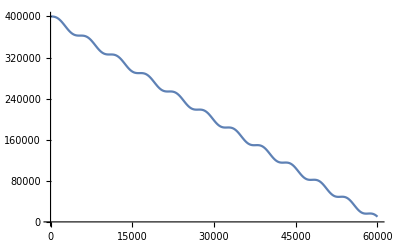

Speed:

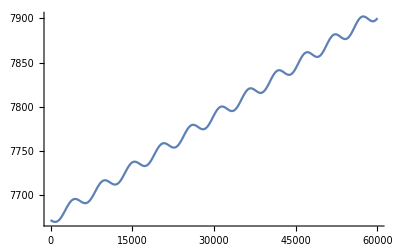

Energy:

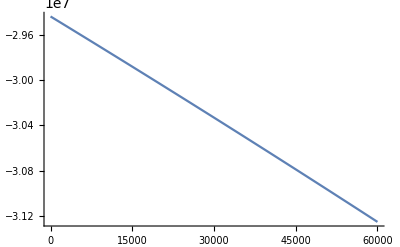

Orbital Trajectory:

```mathematica
m=420000;
M=5972*10^21;
G=6674*10^-14;
r=6371000;
A=1/2000000;
B=100000000;
Fx=A(1000000HeavisidePi[Sqrt[x[t]^2+y[t]^2]/(2r)]+Exp[(r^2-x[t]^2-y[t]^2)/B^2]);
Fy=A(1000000HeavisidePi[Sqrt[x[t]^2+y[t]^2]/(2r)]+Exp[(r^2-x[t]^2-y[t]^2)/B^2]);

Needs["VariationalMethods`"]
s=NDSolve[{{((G*M*x[t])/(x[t]^2+y[t]^2)^(3/2))+x''[t]+x'[t]Fx==0,((G*M*y[t])/(x[t]^2+y[t]^2)^(3/2))+y''[t]+y'[t]Fy==0},x[0]==6771000,y[0]==0,x'[0]==0,y'[0]==7672},{x,y},{t,0,60000}]
"Height:"
Plot[Evaluate[{Sqrt[x[t]^2+y[t]^2]-r}/.s],{t,0,60000}]
"Speed:"
Plot[Evaluate[{Sqrt[x'[t]^2+y'[t]^2]}/.s],{t,0,60000}]
"Energy:"
Plot[Evaluate[{(x'[t]^2+y'[t]^2)/2-G M/Sqrt[x[t]^2+y[t]^2]}/.s],{t,0,60000}]

"Orbital Trajectory:"
plt=Plot[-8371000,{x,-7371000,7371000},PlotRange->{-7371000,7371000},AxesStyle->{Directive[0,Black],Directive[0,Black]},Ticks->None,Axes->{False,False}];
Animate[Show[plt,Graphics[{Red,Ball[{x[t],y[t]},100000]}],Graphics[{Green,Ball[{0,0},6371000]}],AspectRatio->Automatic]/.s,{t,0,60000},AnimationRate->3000, AnimationRunning->False,RefreshRate->120]
```